# Ans to the question no : 6

## (a)

```mathematica
DSolve[(ⅇ^x + ⅇ^-x) y'[x] == (y[x])^2, y[x], x]
```

{{y[x]→1/(-ArcTan[ⅇ^x]-C[1])}}

```mathematica
sol = y[x] /. %21 /. C[1] -> a
```

{1/(-a-ArcTan[ⅇ^x])}

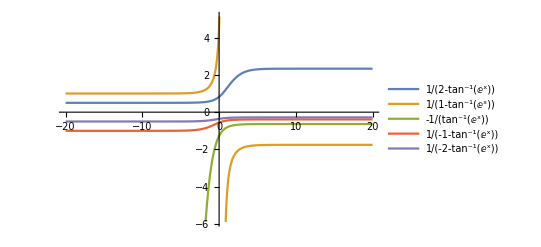

```mathematica
Plot[Evaluate[Table[sol, {a, -2, 2}]], {x, -20, 20}, PlotLegends->"Expressions", PlotStyle->Thick]
```

## (b)

```mathematica
DSolve[{y''[x] + y[x] == 0, y[0] == 1, y[π/2] == 1}, y[x], x]
```

{{y[x]→Cos[x]+Sin[x]}}

```mathematica
y[x]/. %41[[1]] /. x-> π
```

-1

## (c)

```mathematica
NDSolve[{y''[x] + x y[x]-y[x] == 0, y'[0] == 1, y[1] == -1}, y[x], {x, 0, 10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

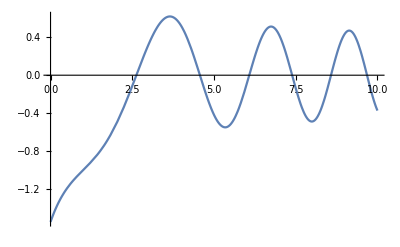

```mathematica
Plot[y[x] /. %45, {x, 0, 10}]
```